# Two-way capacity for MAD channels

```mathematica
Needs["QuantumUtils`"]
Needs["MaTeX`"]
AddAssumption[assumption_]:=$Assumptions=DeleteDuplicates[$Assumptions&&assumption];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
```

## Setting

### Dimension

Set the dimension of the Hilbert Space

```mathematica
d=3;
```

### Input state

Build diagonal density matrix with trigonometric parametrization

```mathematica
BuildDensity[par_]:=(
ρSys = ConstantArray[0,{d,d}];
Do[
ρSys[[j1,j1]]=Product[(Sin[ToExpression[ToString[par]<>ToString[j2-1]]])^2,{j2,1,j1-1}]*(Cos[ToExpression[ToString[par]<>ToString[j1-1]]])^2,
{j1,1,d-1}
];
ρSys[[d,d]]=Product[(Sin[ToExpression[ToString[par]<>ToString[j2-1]]])^2,{j2,1,d-1}];
Simplify[ρSys]
)
BuildDensityDim[par_,dim_]:=(
ρSys = ConstantArray[0,{dim,dim}];
Do[
ρSys[[j1,j1]]=Product[(Sin[ToExpression[ToString[par]<>ToString[j2-1]]])^2,{j2,1,j1-1}]*(Cos[ToExpression[ToString[par]<>ToString[j1-1]]])^2,
{j1,1,dim-1}
];
ρSys[[dim,dim]]=Product[(Sin[ToExpression[ToString[par]<>ToString[j2-1]]])^2,{j2,1,dim-1}];
Simplify[ρSys]
)
```

### Transition matrices

Build transition matrix - standard form

```mathematica
GammaMat[par_]:=(
gam =IdentityMatrix[d];
Do[
Do[
AddAssumption[Element[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],Reals]];
AddAssumption[0<=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]]<=1];
gam[[j,i]]=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],
{i,1,j-1}
];
AddAssumption[0<=1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}]<=1];
gam[[j,j]] =1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}],
{j,1,d}
];
gam//Simplify
);
GammaMatDim[par_,dim_]:= (
gam =IdentityMatrix[dim];
Do[
Do[
AddAssumption[Element[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],Reals]];
AddAssumption[0<=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]]<=1];
gam[[j,i]]=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],
{i,1,j-1}
];
AddAssumption[0<=1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}]<=1];
gam[[j,j]] =1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}],
{j,1,dim}
];
gam//Simplify
);
```

Function that clears symbols associated to amplitudes parametrized by par

```mathematica
ClearAmplitudes[par_]:=(
Do[
ToExpression[ToString[par]<>ToString[j]<>ToString[i],InputForm,Clear],
{j,1,d},{i,0,j-1}
]
)
```

## Kraus operators

### Build Kraus operators

Maximum number of Kraus operators

```mathematica
nKmax = d (d-1)/2 +1;
```

ij elements

```mathematica
Krausij[mat_, in1_,in2_]:=(
dim=Length[mat];
kr = ConstantArray[0,{dim,dim}];
kr[[in1,in2]]=Sqrt[mat[[in2,in1]]]; 
Simplify[kr]
);
```

00 element

```mathematica
Kraus00[mat_]:=(
dim=Length[mat];
kr= IdentityMatrix[dim]; 
Do[
kr[[jj,jj]]=Sqrt[mat[[jj,jj]]],
{jj,1,dim}
];
Simplify[kr]
);
```

List of Kraus operators

```mathematica
KrausList[mat_]:=(
dim=Length[mat];
KrausListTMP={};
AppendTo[KrausListTMP,Kraus00[mat]];
Do[
AppendTo[KrausListTMP,Krausij[mat, in1,in2]],
{in2,2,dim},{in1,1,in2-1}
];
Simplify[KrausListTMP]
)
```

Number of non-zero Kraus operators

```mathematica
nK[mat_]:=Length[KrausList[mat]];
```

## MAD channel

```mathematica
MAD[par_]:=Kraus[KrausList[GammaMat[par]]]
```

## ADC

```mathematica
ADC[par_]:=(
AddAssumption[0<=par<=1];
AddAssumption[0<=1-par<=1];
Krausadc={{{1,0},{0,Sqrt[1-par]}},{{0,Sqrt[par]},{0,0}}};
Kraus[Krausadc]//Simplify
)
```

## Complementary channel

```mathematica
KrausTrace[θ_,M1_,M2_] := Simplify[Tr[M1.θ.ConjugateTranspose[M2]]];
ComplMAD[θ_,chan_]:=(
dimEnv = Length[chan[[1]]];
krausset=chan[[1]];
th =ConstantArray[0,{dimEnv,dimEnv}];
Do[
th[[i,j]]=KrausTrace[θ,chan[[1,i]],chan[[1,j]]],
{i,1,dimEnv},{j,1,dimEnv}
];
Simplify[th]
);
```

## Choi Matrix

Function to generate Choi matrix of an input channel, written from scratch

```mathematica
ChoiMatrix[ch_]:=(

dimOut=OutputDim[ch];
choi=ConstantArray[0,{d*dimOut,d*dimOut}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[i,j]]=1;
dmprime=ch[dm];
dm[[i,j]]=0;
Do[
choi[[(i-1)*dimOut+i1,(j-1)*dimOut+j1]]=dmprime[[i1,j1]],
{j1,1,dimOut},{i1,1,dimOut}
],
{i,1,d},{j,1,d}
];

choi/d
)
```

## Entropy and Coherent Information

```mathematica
Unprotect[Log];
Log[0|0.]=0;
Protect[Log];
s[x_]:=-x*Log[x];
```

### Define Von Neumann Entropy function

```mathematica
EntropyVN[mat_]:=(
ei=Eigenvalues[mat];
dim=Dimensions[mat][[1]];
en=0;
Do[
en=en+s[ei[[ij]]],
{ij,1,dim}
];
en/Log[2]//Simplify
)
```

### Define Coherent Information function

```mathematica
InfoC[den_,chan_]:=(
outstate=chan[den];
envstate=ComplMAD[den,chan];
ic=EntropyVN[outstate]-EntropyVN[envstate];
ic
)
```

### Define Mutual Information function

This function computes the mutual information of a channel chan, given the input state den

```mathematica
InfoM[den_,chan_]:=(
outstate=chan[den];
envstate=ComplMAD[den,chan];
im=EntropyVN[den]+EntropyVN[outstate]-EntropyVN[envstate];
Simplify[im]
)
```

### Reverse Coherent Information

```mathematica
InfoRC[gam_]:=(
KrausSet=KrausList[gam];
chan=Kraus[KrausSet];
ρϕ=ChoiMatrix[chan];
icr=Log2[d]-EntropyVN[ρϕ];
Simplify[icr]
)
```

```mathematica
ReverseInfoChoi[chan_]:=(
ρϕ=ChoiMatrix[chan];
icr=Log2[d]-EntropyVN[ρϕ];
Simplify[icr]
)
```

## PPT criterion

```mathematica
PartialTransposeChoi[ch_]:=(
dimOut=OutputDim[ch];
choi=ConstantArray[0,{d*dimOut,d*dimOut}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[i,j]]=1;
dmprime=ch[dm];
dm[[i,j]]=0;
Do[
choi[[(i-1)*dimOut+i1,(j-1)*dimOut+j1]]=dmprime[[j1,i1]],
{j1,1,dimOut},{i1,1,dimOut}
],
{i,1,d},{j,1,d}
];
choi/d
)
```

```mathematica
ΓGen=GammaMat[g];
KrausSetGen=KrausList[ΓGen];
MADGen=Kraus[KrausSetGen];
ρϕt=PartialTransposeChoi[MADGen];
ρϕ=Choi[MADGen];
EiChoiTr=Simplify[Eigenvalues[ρϕt]]
EiChoi=Simplify[Eigenvalues[ρϕ]]
```

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[True].

{1/3,1/3,(1-g10)/3,1/3 (-1+g10),1/3 (1-g20-g21),1/6 (g20-√(g20^2-4 (-1+g20+g21))),1/6 (g20+√(g20^2-4 (-1+g20+g21))),1/6 (g21-√(g21^2+4 (-1+g10) (-1+g20+g21))),1/6 (g21+√(g21^2+4 (-1+g10) (-1+g20+g21)))}

{0,0,0,0,0,g10,g20,3-g10-g20-g21,g21}

```mathematica
g10=1;

EiChoiTr//Simplify
EiChoi
```

{1/3,1/3,0,0,1/3 (1-g20-g21),1/6 (g20-√(g20^2-4 (-1+g20+g21))),1/6 (g20+√(g20^2-4 (-1+g20+g21))),0,g21/3}

{0,0,0,0,0,1,g20,2-g20-g21,g21}

## Teleportation unitaries

### Build list

```mathematica
TeleUnitary[a_,b_]:=(
Z=ConstantArray[0,{d,d}];
X=ConstantArray[0,{d,d}];
Do[
Z[[k+1,k+1]]=Exp[I*2*Pi*k*b/d];
X[[Mod[k+a,d]+1,k+1]]=1,
{k,0,d-1}
];
X.Z
)

TeleList1[in_]:=(
a=Floor[(in-1)/d];
b=Mod[in-1,d];
TeleUnitary[a,b]
)

TeleList=Table[TeleList1[in],{in,1,9}];
```

```mathematica
ChoiMAD=ChoiMatrix[MAD[γ]];
ChoiCommutator[in1_,in2_]:=KroneckerProduct[Conjugate[TeleList[[in1]]],TeleList[[in2]]].ChoiMAD-ChoiMAD.KroneckerProduct[Conjugate[TeleList[[in1]]],TeleList[[in2]]];

Table[ChoiCommutator[4,n],{n,Length[TeleList]}][[9]]//MatrixForm//Simplify
```

(0 | 0 | -1/3 (-1)^(2/3) √(1-γ10) | -1/3 √(1-γ20-γ21) | 0 | 0 | 0 | -1/3 (-1)^(1/3) (-1+γ21) | 0
1/3 (-1)^(2/3) √(1-γ20-γ21) | 0 | 0 | 0 | 1/3 (-1)^(2/3) √((-1+γ10) (-1+γ20+γ21)) | 0 | 0 | 0 | -1/3 (-1)^(2/3) (-1+γ20+γ21)
0 | 0 | 0 | 0 | 0 | 0 | γ20/3 | 0 | 0
0 | 1/3 (-1)^(1/3) γ10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/3 (-1)^(2/3) (-1+γ10) | -1/3 √((-1+γ10) (-1+γ20+γ21)) | 0 | 0 | 0 | 1/3 (-1)^(1/3) √(1-γ10) | 0
1/3 | 0 | 0 | 0 | (√(1-γ10))/3 | 0 | 0 | 0 | 1/3 √(1-γ20-γ21)
-1/3 (-1)^(1/3) √(1-γ10) | 0 | 0 | 0 | 1/3 (-1)^(1/3) (-1+γ10+γ20) | 0 | 0 | 0 | -1/3 (-1)^(1/3) √((-1+γ10) (-1+γ20+γ21))
0 | 0 | 0 | 0 | 0 | -1/3 (-1)^(2/3) γ21 | 0 | 0 | 0
0 | 0 | -1/3 (-1)^(2/3) √((-1+γ10) (-1+γ20+γ21)) | 1/3 (-1+γ10+γ20+γ21) | 0 | 0 | 0 | 1/3 (-1)^(1/3) √(1-γ20-γ21) | 0)

MAD channels are not weyl covariant

## Computations

```mathematica
texStyle={FontSize->12};
icadc[x_]=InfoC[BuildDensityDim[θ,2],ADC[x]];
iccadc[x_]:=NMaximize[icadc[x],{θ0}][[1]];
```

```mathematica
ρD=BuildDensity[θ];
Γ=GammaMat[γ];
```

### (1A3) Single decay

```mathematica
γ//ClearAmplitudes;
γ21=0;
γ20=0;
```

```mathematica
ic1a3=InfoC[ρD,Kraus[KrausList[GammaMat[γ]]]];
icc1a3[γ10_]:=NMaximize[ic1a3,{θ0,θ1}][[1]];
```

```mathematica
ichoir1a3[γ10_]=Simplify[ReverseInfoChoi[Kraus[KrausList[GammaMat[γ]]]]];
```

```mathematica
tex11=MaTeX["Q\\left(\\Phi ^{(3)} _{\\Gamma_{\\mathrm{1A3}} (\\gamma _{10},0,0)}\\right)",Magnification->1.5];
tex12=MaTeX["I _{RC}\\left(\\bar{\\rho},\\Phi ^{(3)} _{\\Gamma_{\\mathrm{1A3}} (\\gamma _{10},0,0)}\\right)",Magnification->1.5];
```

```mathematica
plot1a3sub1=Plot[
{icc1a3[γ10],ichoir1a3[γ10]},
{γ10,0,1/2},
PlotLegends->Placed[
LineLegend[{tex11,tex12},LegendFunction->(Framed[#,Background->White,RoundingRadius->4]&)],
{Right,Top}
]
];
```

```mathematica
plot1a3sub2=Plot[{1,ichoir1a3[γ10]},{γ10,1/2,1}];
```

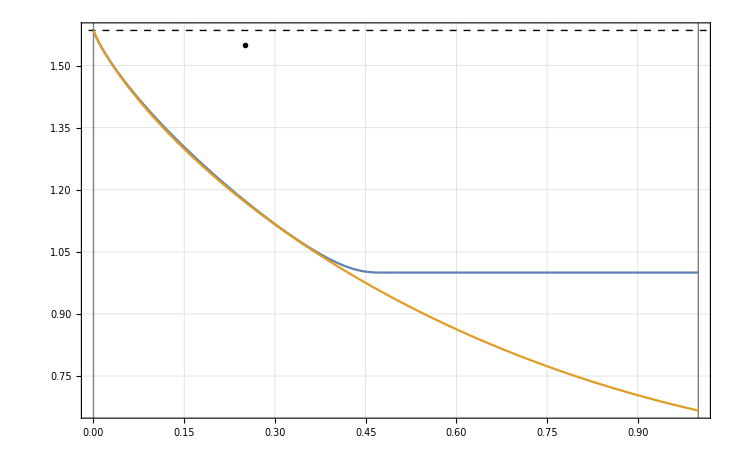

```mathematica
Show[
plot1a3sub1,
plot1a3sub2,
FrameLabel->{
MaTeX["\\gamma _{10}",Magnification->1.5]
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
AxesOrigin->{0,0.6},
PlotRange->All,
GridLines->Automatic,
Prolog->{
{
Directive[Thin,Gray],
Line[{{1,0.5},{1,1.7}}],
Line[{{0,0.5},{0,1.7}}]
},
{
Directive[Dashed,Thin,Black],
Line[{{-0.1,Log2[3]},{1.1,Log2[3]}}]
},
{
Directive[Dashed,Thin,Black],
Text[MaTeX["\\color{black} \\log _2 3",Magnification->1.4],{0.25,1.55}]
}
},
BaseStyle->texStyle
]
```

### (2A3) γ_(2,1)=0

```mathematica
γ//ClearAmplitudes;
γ21=0;
```

```mathematica
ic2a3=InfoC[ρD,Kraus[KrausList[GammaMat[γ]]]];
icc2a3[γ10_,γ20_]:=NMaximize[ic2a3,{θ0,θ1}][[1]];
```

```mathematica
ichoir2a3[γ10_,γ20_]=ReverseInfoChoi[Kraus[KrausList[GammaMat[γ]]]];
```

```mathematica
tex2a31=MaTeX["Q\\left(\\Phi ^{(3)} _{\\Gamma_{\\mathrm{2A3}} (\\gamma _{10},\\gamma _{20},0)}\\right)",Magnification->1.5];
tex2a32=MaTeX["I _{RC}\\left(\\bar{\\rho},\\Phi ^{(3)} _{\\Gamma_{\\mathrm{2A3}} (\\gamma _{10},\\gamma _{20},0)}\\right)",Magnification->1.5];
```

```mathematica
plot2a3sub1=DensityPlot[
Max[icc2a3[γ10,γ20],ichoir2a3[γ10,γ20]],
{γ10,0,1/2},{γ20,0,1/2},
ColorFunction->ColorData[{"StarryNightColors",{0,Log[3]/Log[2]}}],
ColorFunctionScaling->False
];
```

```mathematica
plot2a3sub12=Plot3D[
{icc2a3[γ10,γ20],ichoir2a3[γ10,γ20]},
{γ10,0,1/2},{γ20,0,1/2},
PlotLegends->{tex2a31,tex2a32},
PlotStyle->{{Orange,Opacity[0.7]}, {Blue,Opacity[0.7]}}
];
```

```mathematica
plot2a3sub2=DensityPlot[
Max[iccadc[γ10],ichoir2a3[γ10,γ20]],
{γ10,0,1/2},{γ20,1/2,1},
ColorFunction->ColorData[{"StarryNightColors",{0,Log[3]/Log[2]}}],
ColorFunctionScaling->False
];
```

```mathematica
plot2a3sub22=Plot3D[
{iccadc[γ10],ichoir2a3[γ10,γ20]},
{γ10,0,1/2},{γ20,1/2,1},
PlotStyle->{{Orange,Opacity[0.7]}, {Blue,Opacity[0.7]}}
];
```

```mathematica
plot2a3sub3=DensityPlot[
Max[iccadc[γ20],ichoir2a3[γ10,γ20]],
{γ10,1/2,1},{γ20,0,1/2},
ColorFunction->ColorData[{"StarryNightColors",{0,Log[3]/Log[2]}}],
ColorFunctionScaling->False
];
```

```mathematica
plot2a3sub32=Plot3D[
{iccadc[γ20],ichoir2a3[γ10,γ20]},
{γ10,1/2,1},{γ20,0,1/2},
PlotStyle->{{Orange,Opacity[0.7]}, {Blue,Opacity[0.7]}}
];
```

```mathematica
plot2a3sub4=DensityPlot[
Max[0,ichoir2a3[γ10,γ20]],
{γ10,1/2,1},{γ20,1/2,1},
ColorFunction->ColorData[{"StarryNightColors",{0,Log[3]/Log[2]}}],
ColorFunctionScaling->False
];
```

```mathematica
plot2a3sub42=Plot3D[
{0,ichoir2a3[γ10,γ20]},
{γ10,1/2,1},{γ20,1/2,1},
PlotStyle->{{Orange,Opacity[0.7]}, {Blue,Opacity[0.7]}}
];
```

```mathematica
Show[
plot2a3sub12,
plot2a3sub22,
plot2a3sub32,
plot2a3sub42,
Frame->{{True,True},{True,True}},
AxesLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["\\gamma _{20}",Magnification->1.7],
MaTeX["Q_2 \\textrm{ lower bound}",Magnification->1.7],
},
RotateLabel->False,
PlotRange->All,
PlotLegends->Automatic,
BaseStyle->texStyle,
]
```

### (2B3)γ_(1,0)=0

```mathematica
γ//ClearAmplitudes;
γ10=0;
```

```mathematica
ic2b3=Simplify[InfoC[ρD,Kraus[KrausList[GammaMat[γ]]]]];
icc2b3[γ21_,γ20_]:=NMaximize[ic2b3,{θ0,θ1}][[1]]
```

```mathematica
ichoir2b3[γ21_,γ20_]=ReverseInfoChoi[Kraus[KrausList[GammaMat[γ]]]];
```

```mathematica
tex2b31=MaTeX["Q\\left(\\Phi ^{(3)} _{\\Gamma_{\\mathrm{2B3}} (0,\\gamma _{20},\\gamma _{21})}\\right)",Magnification->1.5];
tex2b32=MaTeX["I _{RC}\\left(\\bar{\\rho},\\Phi ^{(3)} _{\\Gamma_{\\mathrm{2B3}} (0,\\gamma _{20},\\gamma _{21})}\\right)",Magnification->1.5];
```

```mathematica
plot2b3sub1=DensityPlot[
Max[icc2b3[γ21,γ20],ichoir2b3[γ21,γ20]],
{γ21,0,1/2},{γ20,0,1/2-γ21},
ColorFunction->ColorData[{"StarryNightColors",{1,Log[3]/Log[2]}}],
ColorFunctionScaling->False
];
```

```mathematica
plot2b3sub12=Plot3D[
{icc2b3[γ21,γ20],ichoir2b3[γ21,γ20]},
{γ20,0,1/2},{γ21,0,1/2-γ20},
PlotLegends->{tex2b31,tex2b32},
PlotStyle->{{Orange,Opacity[0.7]}, {Blue,Opacity[0.7]}}
];
```

```mathematica
plot2b3sub2=DensityPlot[
Max[1,ichoir2b3[γ21,γ20]],
{γ21,0,1},{γ20,Max[1/2-γ21,0],1-γ21},
ColorFunction->ColorData[{"StarryNightColors",{1,Log[3]/Log[2]}}],
ColorFunctionScaling->False
];
```

```mathematica
plot2b3sub22=Plot3D[
{1,ichoir2b3[γ21,γ20]},
{γ21,0,1},{γ20,Max[1/2-γ21,0],1-γ21},
PlotStyle->{{Orange,Opacity[0.7]}, {Blue,Opacity[0.7]}}
];
```

```mathematica
Show[
plot2b3sub12,
plot2b3sub22,
AxesLabel->{
MaTeX["\\gamma _{20}",Magnification->1.7],
MaTeX["\\gamma _{21}",Magnification->1.7],
MaTeX["Q_2 \\textrm{ lower bound}",Magnification->1.7],
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
PlotRange->All,
PlotLegends->Automatic,
BaseStyle->texStyle
]
```

### (d)γ_(2,0)=0

```mathematica
γ//ClearAmplitudes;
γ20=0;
```

```mathematica
ic2c3=Simplify[InfoC[ρD,Kraus[KrausList[GammaMat[γ]]]]];
icc2c3[γ10_,γ21_]:=NMaximize[ic2c3,{θ0,θ1}][[1]]
```

```mathematica
ichoir2c3[γ10_,γ21_]=ReverseInfoChoi[Kraus[KrausList[GammaMat[γ]]]];
```

```mathematica
tex2c31=MaTeX["\\max _{\\rho ^{(diag)}}I_C\\left(\\rho ^{(diag)},\\Phi ^{(3)} _{\\Gamma_{\\mathrm{2C3}} (\\gamma _{10},0,\\gamma _{21})}\\right)",Magnification->1.5];
tex2c32=MaTeX["I _{RC}\\left(\\bar{\\rho},\\Phi ^{(3)} _{\\Gamma_{\\mathrm{2C3}} (\\gamma _{10},0,\\gamma _{21})}\\right)",Magnification->1.5];
```

```mathematica
plot2c3sub1=DensityPlot[
Max[icc2c3[γ10,γ21],ichoir2c3[γ10,γ21]],
{γ10,0,1},{γ21,0,1},
ColorFunction->ColorData[{"StarryNightColors",{0,Log[3]/Log[2]}}],
ColorFunctionScaling->False
];
```

```mathematica
plot2c3sub12=Plot3D[
{icc2c3[γ10,γ21],ichoir2c3[γ10,γ21]},
{γ10,0,1},{γ21,0,1},
PlotLegends->{tex2c31,tex2c32},
PlotStyle->{{Orange,Opacity[0.7]}, {Blue,Opacity[0.7]}}
];
```

```mathematica
Show[
plot2c3sub12,
AxesLabel->{
MaTeX["\\gamma _{10}",Magnification->1.7],
MaTeX["\\gamma _{21}",Magnification->1.7],
MaTeX["Q_2 \\textrm{ lower bound}",Magnification->1.7],
},
RotateLabel->False,
Frame->{{True,True},{True,True}},
PlotRange->All,
GridLines->None,
PlotLegends->Automatic,
BaseStyle->texStyle
]
```